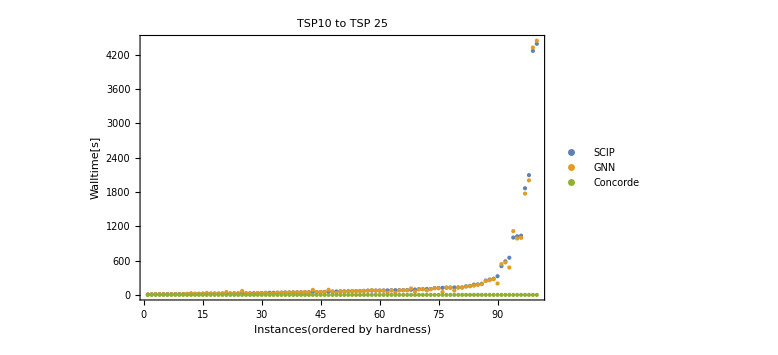

2.86023

```mathematica
data=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/10-on-25n.csv", Numeric->True];concorde=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/concorde/25n_0423-1623.csv", Numeric->True];
data=Delete[data, 1];
concorde=Delete[concorde,1];
{baseline, gnn}=GatherBy[data,First];
baseline=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@baseline);
gnn=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@gnn);
(*{stime|walltime|proctime}*)
baselineWall=Part[#,2]&/@baseline;
gnnWall=Part[#,2]&/@gnn;
concorde=Part[#,2]&/@concorde;
{baselineWall,gnnWall,concorde}=SortBy[{baselineWall,gnnWall,concorde}ᵀ,First]ᵀ;
plot=Show[
ListPlot[{baselineWall,gnnWall,concorde},
Frame->True, FrameLabel->{"Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN","Concorde"}],{0.1,0.85}]],
PlotRange->{Automatic,{Max[Floor[Min[baselineWall,gnnWall,concorde]],0],Ceiling[Max[baselineWall,gnnWall]]+1}},
PlotLabel->Style["TSP10 to TSP 25"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/15-25/normal.png",plot];Mean[baselineWall-gnnWall]/Mean[baselineWall]*100
```

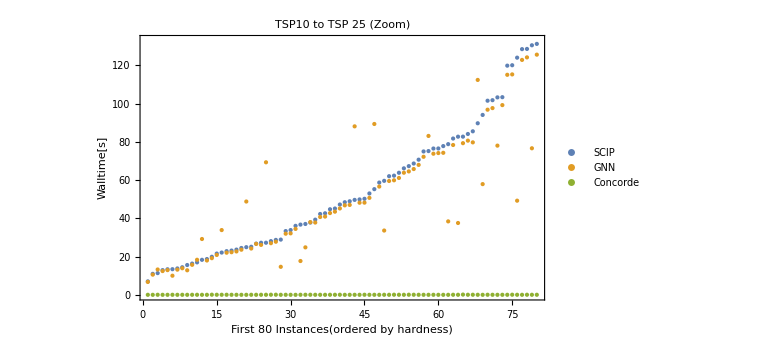

6.52484

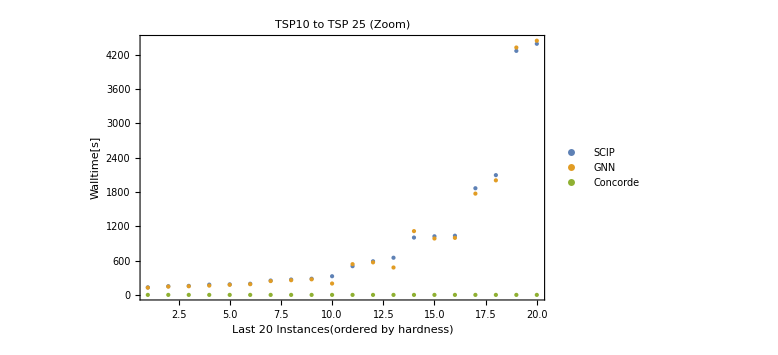

2.04938

```mathematica
plot1=Show[
ListPlot[{baselineWall[[1;;80]],gnnWall[[1;;80]],concorde[[1;;80]]},
Frame->True, FrameLabel->{"First 80 Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN","Concorde"}],{0.1,0.85}]],
PlotRange->{Automatic,{Max[Floor[Min[baselineWall[[1;;80]],gnnWall[[1;;80]],concorde[[1;;80]]]],0],Ceiling[Max[baselineWall[[1;;80]],gnnWall[[1;;80]]]]+1}},
PlotLabel->Style["TSP10 to TSP 25 (Zoom)"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/15-25/zoom-first80.png",plot1];
Mean[baselineWall[[1;;80]]-gnnWall[[1;;80]]]/Mean[baselineWall[[1;;80]]]*100
plot2=Show[
ListPlot[{baselineWall[[81;;100]],gnnWall[[81;;100]],concorde[[81;;100]]},
Frame->True, FrameLabel->{"Last 20 Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN","Concorde"}],{0.1,0.85}]],
PlotRange->{Automatic,{Max[Floor[Min[baselineWall[[81;;100]],gnnWall[[81;;100]],concorde[[81;;100]]]],0],Ceiling[Max[baselineWall[[81;;100]],gnnWall[[81;;100]]]]+1}},
PlotLabel->Style["TSP10 to TSP 25 (Zoom)"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/15-25/zoom-last20.png",plot2];
Mean[baselineWall[[81;;100]]-gnnWall[[81;;100]]]/Mean[baselineWall[[81;;100]]]*100
```